```mathematica
ResourceFunction["DarkMode"][]
```

Colour Templates

```mathematica
rybColourRules = {0->Red,1->Yellow,2->Blue};
rybDarkColourRules = "DarkRainbow";
fancyColourRules = "CandyColors";
blueColourRules = "DeepSeaColors";
pinkColourRules = "ValentineTones";
orangeColourRules = "SolarColors";
tigerColourRules = "SunsetColors";

displaySwatch[colourFunction_] := ArrayPlot[Mod[generateMaxHeightGrid[21],3], ColorFunction->colourFunction]

displaySwatches[] := Module[{gradients = ColorData["Gradients"], len = Length[ColorData["Gradients"]], swatches = {}, i = 0}, 
	Grid[ArrayReshape[Nest[Append[#, displaySwatch[gradients[[i++]]]] &, swatches, len + 1],{Ceiling[len / 6],6}]]]

(*displaySwatches[]*)
```

The following codeblock contains functions that will be evaluated either at the beginning or at the end of the simulation. They generate min/max height grids, and go between 3-coloured grids to height grids.

```mathematica
(* Generate the 'empty' grid with only the boundary cells filled in. Internal cells carry the value -1. *)
initialGridBorder[dim_] := initialGridBorder[dim] = Normal[SparseArray[{{i_, j_} /; i == 1 || j == 1 -> i + j - 2, {i_, j_} /; i == dim || j == dim -> 2dim - i - j}, {dim, dim}, -1]]

(* Helper function for generateMaxHeightGrid. Fills one concentric square of cells. *)
fillConcentricSquareMax[Hold[grid_], k_] := (
 grid[[k, k ;; -k]] = grid[[k - 1, k ;; -k]] + 1; 
 grid[[-k, k ;; -k]] = grid[[-(k - 1), k ;; -k]] + 1;
 grid[[k ;; -k, k]] = grid[[k ;; -k, k - 1]] + 1; 
 grid[[k ;; -k, -k]] = grid[[k ;; -k, -(k - 1)]] + 1; 
ReleaseHold[Hold[grid]])

(* Helper function for generateMinHeightGrid. Fills one concentric square of cells. *)
fillConcentricSquareMin[Hold[grid_], k_] := (
 grid[[k, k ;; -k]] = grid[[k - 1, k ;; -k]] - 1; 
 grid[[-k, k ;; -k]] = grid[[-(k - 1), k ;; -k]] - 1;
 grid[[k ;; -k, k]] = grid[[k ;; -k, k - 1]] - 1; 
 grid[[k ;; -k, -k]] = grid[[k ;; -k, -(k - 1)]] - 1; 
ReleaseHold[Hold[grid]])

(* Generates the grid with maximum height by starting from the boundary and moving inwards, filling in concentric squares. *)
generateMaxHeightGrid[dim_] := generateMaxHeightGrid[dim] = Module[{k = 1, depth = (dim + 1) / 2},
 Nest[( k++; currGrid = #; fillConcentricSquareMax[Hold[currGrid], k]; initialGrid = currGrid ) &, initialGrid = initialGridBorder[dim], depth - 1];
 Normal[initialGrid]
]

(* Generates the grid with minimum height by starting from the boundary and moving inwards, filling in concentric squares. *)
generateMinHeightGrid[dim_] := generateMinHeightGrid[dim] = Module[{k = 1, depth = (dim + 1) / 2},
 Nest[( k++; currGrid = #; fillConcentricSquareMin[Hold[currGrid], k]; initialGrid = currGrid ) &, initialGrid = initialGridBorder[dim], depth - 1];
 Normal[initialGrid]
]

(* Takes a grid with a filled in height function as input and converts it to its corresponding 3-colouring form. *)
to3Colouring[grid_] := Mod[grid, 3]

(* Helper function for toHeightFunction *)
findListHeight[first_, list_, len_] := Module[{initialList = SparseArray[{}, {len}, -1], k = 0, prev = first}, (* remember that list is of length (len + 1) *)
 Nest[(k++; newList = #; prev = If[MemberQ[list[[{k, k + 1}]], 1], prev + list[[k + 1]] - list[[k]], If[list[[k]] == 2, prev + 1, prev - 1]]; newList[[k]] = prev; newList ) & , Normal[initialList], len]
]

(* Takes a 3-coloured grid as input and returns the corresponding grid labelled with its height values. *)
(* Edit: we now convert our grid to a 3-coloured grid before computing, so it gives the correct output on every grid! *)
(* Note: this starts with the initial border grid *)
toHeightFunction[grid_] := Module[{heightGrid = initialGridBorder[dim], k = 1, cgrid = to3Colouring[grid]},
  Nest[(k++; nextHeightGrid = #; nextHeightGrid[[k, 2 ;; -2]] = findListHeight[heightGrid[[k, 1]], Normal[cgrid[[k, 1 ;; -2]]], dim - 2]; nextHeightGrid) &, heightGrid, dim - 2] 
] 

(* Calculates the sum of absolute differences between the heights of corresponding sites in the input grids *)
checkHeightDifference[maxGrid_, minGrid_] := Total[Table[Abs[maxGrid[[i, j]] - minGrid[[i, j]]], {i, 2, dim - 1}, {j, 2, dim - 1}], 2]

(* Format time *)
displayTime[time_] := DateString[time, {"Hour", ":", "Minute", ":", "Second"}]

(****** Display Functions ******)

(* Displays height grid matrix in array form *)
displayHeightGrid[grid_] := ArrayPlot[grid, ColorFunction->"GrayTones"]

(* Displays height grid matrices in array form *)
displayHeightGrids[grid1_, grid2_] := Grid[{{displayHeightGrid[grid1], displayHeightGrid[grid2]}}]

(* Displays height grid matrix in array form *)
displayColouringGrid[grid_, colourFunction_] := ArrayPlot[grid, ColorFunction->colourFunction]

(* Displays height grid matrices in array form *)
displayColouringGrids[grid1_, grid2_, colourFunction_] := Grid[{{displayColouringGrid[grid1, colourFunction], displayColouringGrid[grid2, colourFunction]}}]
```

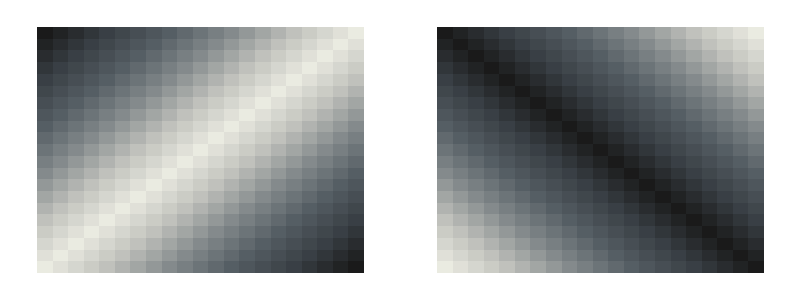

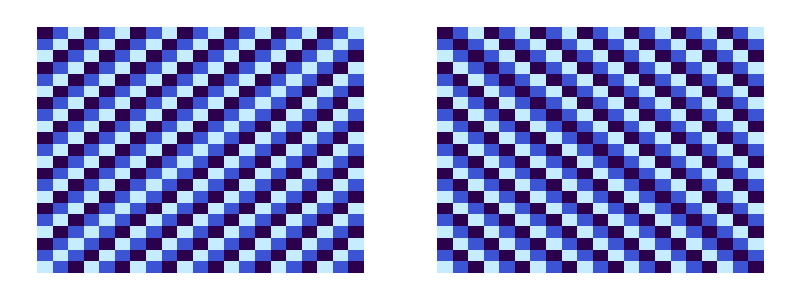

```mathematica
displayHeightGrids[generateMaxHeightGrid[21],generateMinHeightGrid[21]]
displayColouringGrids[to3Colouring[generateMaxHeightGrid[21]], to3Colouring[generateMinHeightGrid[21]], blueColourRules]
```

Uncomment lines to view figures of grids and matrices.

```mathematica
(* Initial boundary grid with empty interior *)
Manipulate[{3(2k - 1), ArrayPlot[initialGridBorder[3(2k - 1)]]},{k,1,20,1}]

(*(* MaxHeightGrid matrix *)
MatrixForm[generateMaxHeightGrid[7], 7]

(* MaxHeightGrid array height function (black and white gradient) *)
Manipulate[ArrayPlot[generateMaxHeightGrid[3(2k - 1)]],{k,1,10,1}]

(* MaxHeightGrid array 3-colouring (candy colours) *)
Manipulate[ArrayPlot[Mod[generateMaxHeightGrid[3(2k - 1)], 3],  ColorFunction->fancyColourRules], {k,1,10,1}]

(* MinHeightGrid matrix *)
MatrixForm[generateMinHeightGrid[7], 7]

(* MinHeightGrid array height function (black and white gradient) *)
Manipulate[ArrayPlot[generateMinHeightGrid[3(2k - 1)]],{k,1,10,1}]

(* MinHeightGrid array 3-colouring (candy colours) *)
Manipulate[ArrayPlot[Mod[generateMinHeightGrid[3(2k - 1)], 3],  ColorFunction->fancyColourRules], {k,1,10,1}]
*)

(*Manipulate[displayHeightGrids(generateMinHeightGrid(3 (2 k-1)),generateMaxHeightGrid(3 (2 k-1))),{k,1,20,1}]
Manipulate[displayColouringGrids(to3Colouring(generateMinHeightGrid(3 (2 k-1))),to3Colouring(generateMaxHeightGrid(3 (2 k-1))),blueColourRules),{k,1,20,1}]
displayHeightGrids(generateMinHeightGrid(57),generateMaxHeightGrid(57))
ArrayPlot[initialGridBorder(57)]*)
```

```mathematica
selectRandomSite[] := RandomChoice[Tuples[Range[2, dim - 1], 2]];
coinFlip[] := RandomChoice[{True, False}]
changeColour[grid_, pos_, newVal_] := ReplacePart[grid, pos -> newVal]

(* Check if you can pop up a cell at pos in grid. Works on both height values and 3-colourings *)
checkPopUp[grid_, pos_] := AllTrue[grid[[pos[[1]] + {-1, 1}, pos[[2]]]] ~ Join ~ grid[[pos[[1]], pos[[2]] + {-1, 1}]], Mod[grid[[Sequence @@ pos]] - #, 3] == 2 &]
(* Check if you can pop down a cell at pos in grid. Works on both height values and 3-colourings *)
checkPopDown[grid_, pos_] := AllTrue[grid[[pos[[1]] + {-1, 1}, pos[[2]]]] ~ Join ~ grid[[pos[[1]], pos[[2]] + {-1, 1}]], Mod[grid[[Sequence @@ pos]] - #, 3] == 1 &]

(* If heads, check if site can be popped up; otherwise, check if site can be popped down. *)
coinFunctionAssociation = Association[True -> checkPopUp, False -> checkPopDown];
coinSignAssociation = Association[checkPopUp -> Plus, checkPopDown -> Subtract];

(* coinTosses: list of random coin flips in the form of a list checkPopUp, checkPopDown functions *)
(* sites: list of random sites *)
(* generates numSteps new coin tosses and sites and adds them to the the beginning of existing lists *)
extendRandomLists[numSteps_] := (
	coinTosses = Join[Table[coinFunctionAssociation[coinFlip[]], numSteps], coinTosses];
	sites = Join[Table[selectRandomSite[], numSteps], sites];
)

(* 5 Run steps from last element added to the lists to the first element added to the lists *)
(* 6 Check if they converge. If not, go back to #3 *)

(* TODO: Edit this! *)
(* Execute one step of the Markov chain on 3-coloured grid *)
(* OPTIMISATION: maybe put this in the function that performs multiple steps instead of calling it over and over? *)
oneStep[coin_, site_] := Module[{initialGrids = {maxGrid, minGrid}, outGrids = {maxGrid, minGrid}},
   Map[If[coin[initialGrids[[#]], site], 
   (outGrids[[#]] = changeColour[initialGrids[[#]], site, Mod[coinSignAssociation[coin][initialGrids[[#]][[Sequence @@ site]], 2], 3]];)] &, {1, 2}];
   {maxGrid, minGrid} = outGrids;
]
```

Global Variables:
- maxGrid, minGrid
- coinTosses
- sites
- dim

```mathematica
(* testing oneStep *)
dim = 9;
maxGrid = to3Colouring[generateMaxHeightGrid[dim]];
minGrid = to3Colouring[generateMinHeightGrid[dim]];
Map[MatrixForm[#] &, {maxGrid, minGrid}]
oneStep[checkPopDown, {5,5}]
Map[MatrixForm[#] &, {maxGrid, minGrid}]
oneStep[checkPopDown, {4,6}]
Map[MatrixForm[#] &, {maxGrid, minGrid}]
Map[MatrixForm[#] &, {to3Colouring[generateMaxHeightGrid[dim]] - maxGrid, to3Colouring[generateMinHeightGrid[dim]] - minGrid}]
(* conclusion: oneStep works!*)
```

```mathematica
(* testing extendRandomLists *)
arr1 = {};
arr2 = {};
sites = {};
coinTosses = {};
extendRandomLists[10];
Print["first:", sites, coinTosses]
extendRandomLists[10];
Print["second:", sites, coinTosses]
(* conclusion: extendedRandomLists works! *)
```

first:{{2,3},{2,2},{4,4},{2,3},{3,3},{2,2},{4,3},{4,2},{4,4},{3,3}}{checkPopUp,checkPopUp,checkPopUp,checkPopDown,checkPopUp,checkPopUp,checkPopDown,checkPopDown,checkPopDown,checkPopDown}

second:{{4,4},{3,3},{3,3},{2,3},{2,3},{3,3},{2,3},{2,2},{3,4},{2,3},{2,3},{2,2},{4,4},{2,3},{3,3},{2,2},{4,3},{4,2},{4,4},{3,3}}{checkPopDown,checkPopDown,checkPopUp,checkPopUp,checkPopUp,checkPopUp,checkPopUp,checkPopUp,checkPopUp,checkPopUp,checkPopUp,checkPopUp,checkPopUp,checkPopDown,checkPopUp,checkPopUp,checkPopDown,checkPopDown,checkPopDown,checkPopDown}

```mathematica
(* Executes the algorithm for a specified number of steps and displays the result *)
nStepsMarkovChain[maxGrid_, minGrid_, steps_, logInterval_, prevStep_] := Module[{step = prevStep},
  PrintTemporary[ProgressIndicator[Dynamic[step/(steps + prevStep)]]]; {time, finalGrids} = AbsoluteTiming[Catch[Nest[(
  If[Mod[step, logInterval] == 0 || #[[1]] == #[[2]], (Export[StringJoin[ToString[NotebookDirectory[]], "output files/coupling_", ToString[dim], "/log_", ToString[step], ".mx"], #]; 
    Print[checkHeightDifference[n, #[[1]], #[[2]]]])]; 
  If[#[[1]] == #[[2]], Throw[#]]; 
  step++; 
  oneStep[Sequence @@ #]) &, 
  {maxGrid, minGrid}, steps + 1]]];
  {time, step, finalGrids}
]
```

TODO:
- logging into files
- display dynamic progress indicator: height difference, step number, and length of coinTosses

Notes as we write this function:
- catch when the grids become equal
- execute for numsteps = length of coinTosses
- don’t need the prevStep input from last time, nor maxGrid and minGrid and steps. Only logInterval needed!

```mathematica
(* Executes the algorithm for as many steps as required *)
nStepsMarkovChain[] := Module[{numSteps = Length[coinTosses]},
  Catch[
    Nest[(
      If[#[[1]] == #[[2]], Throw[#]];
      oneStep[Sequence @@ #]
    ) &, {maxGrid, minGrid}, numSteps]]
]
```

Remember: 
- each time we restart chain, need to delete logfiles
- need to re-initialise maxGrid and minGrid

{{{0,1,2,0,1,2,0,1,2},{1,2,0,1,2,0,1,2,1},{2,0,1,2,0,1,2,1,0},{0,1,2,0,1,2,1,0,2},{1,2,0,1,2,1,0,2,1},{2,0,1,2,1,0,2,1,0},{0,1,2,1,0,2,1,0,2},{1,2,1,0,2,1,0,2,1},{2,1,0,2,1,0,2,1,0}},{{0,1,2,0,1,2,0,1,2},{1,0,1,2,0,1,2,0,1},{2,1,0,1,2,0,1,2,0},{0,2,1,0,1,2,0,1,2},{1,0,2,1,0,1,2,0,1},{2,1,0,2,1,0,1,2,0},{0,2,1,0,2,1,0,1,2},{1,0,2,1,0,2,1,0,1},{2,1,0,2,1,0,2,1,0}}}

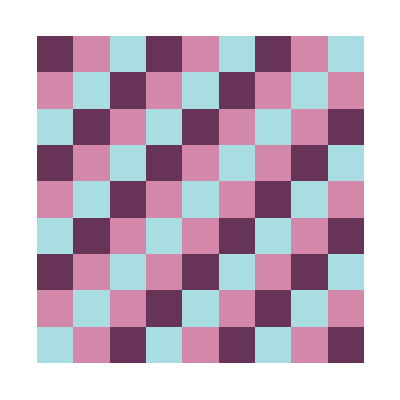
-Graphics- | displayHeightGrid[{{0,1,2,0,1,2,0,1,2},{1,0,1,2,0,1,2,0,1},{2,1,0,1,2,0,1,2,0},{0,2,1,0,1,2,0,1,2},{1,0,2,1,0,1,2,0,1},{2,1,0,2,1,0,1,2,0},{0,2,1,0,2,1,0,1,2},{1,0,2,1,0,2,1,0,1},{2,1,0,2,1,0,2,1,0}},CandyColors]

```mathematica
coinTosses = {};
sites = {};
extendRandomLists[1000];
outGrids = nStepsMarkovChain[]
displayColouringGrids[outGrids[[1]], outGrids[[2]], fancyColourRules]
```

```mathematica
Monitor[For[n = 0, n < 10,  n = n + 1,  Pause[1]],(n, ProgressIndicator[n, {1, 9}])]
```

Syntax::sntxf: "(" cannot be followed by "n,ProgressIndicator[n,{1,9}])".

```mathematica
DynamicModule[{u=0},Dynamic[If[u>100,u=u,u=u+1]]]
```

```mathematica
DynamicModule[{u=0},Dynamic[Refresh[If[u>100,u=u,u=u+1],TrackedSymbols:>{tracker}]]]
```

```mathematica
tracker = 1
```

1

```mathematica
tracker = 2
```

2

```mathematica
Dynamic[{DateString[], Clock[{1,1}, 1]}]
```

```mathematica
Dynamic[{DateString[]}]
```